2 - 10 ODEs reducible to Bessel’s ODE
This is just a sample of such ODEs; some more follow in the next problem set. Find a general solution in terms of J_v and J_-v or indicate when this is not possible. Use the indicated substitutions.

3.  x y''+y'+1/4 y=0  (√x=z)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x y''[x]+y'[x]+1/4 y[x]==0}
```

{y[x]/4+y'[x]+x y''[x]==0}

```mathematica
e2=DSolve[e1,y,x,Assumptions->{√x->z}]
```

{{y→Function[{x},BesselJ[0,√x] C[1]+2 BesselY[0,√x] C[2]]}}

Since Bessel is special function, it takes FullSimplify to simplify it, thereby checking the Mathematica answer.

```mathematica
e1/.e2//FullSimplify
```

{{True}}

The yellow expression above seems to include the text answer, but also a BesselY, which the text answer does not mention. I do not know when, if ever, the BesselY would be useful, but it only takes assigning C[2] to zero to make it go away, leaving the text answer.

```mathematica
e2[[1,1,2]]
```

Function[{x},BesselJ[0,√x] C[1]+2 BesselY[0,√x] C[2]]

```mathematica
gad=e2[[1,1,2]]/.{C[1]->1,C[2]->1}
```

Function[{x},BesselJ[0,√x] 1+2 BesselY[0,√x]]

```mathematica
pl1=Plot[BesselJ[0,√x],{x,0,1},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250];
```

I have to admit, the below plots show that the BesselY does seem to add something to the situation.

```mathematica
pl2=Plot[BesselJ[0,√x] 1+2 BesselY[0,√x],{x,0,1},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250];
```

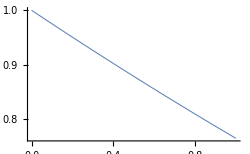
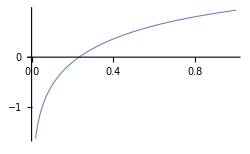

```mathematica
Row[{pl1,pl2}]
```

5.  Two-parameter ODE
x^2 y''+x y'+(λ^2 x^2-ν^2)y=0  (λx=z)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x^2 y''[x]+x y'[x]+(λ^2 x^2-ν^2) y[x]==0}
```

{(x^2 λ^2-ν^2) y[x]+x y'[x]+x^2 y''[x]==0}

```mathematica
e2=DSolve[e1,y,x,Assumptions->{λ x->z}]
```

{{y→Function[{x},BesselJ[ν,x λ] C[1]+BesselY[ν,x λ] C[2]]}}

```mathematica
e1/.e2//FullSimplify
```

{{True}}

The yellow cell above contains a Bessel function of the first kind and one of the second kind, which Mathematica has checked and found correct. The text answer contains the same Bessel of the first kind, but the other half is expressed as one with negative first argument, as shown in the unsuccessful PZQ below.

```mathematica
PossibleZeroQ[BesselJ[ν,x λ] C[1]+BesselY[ν,x λ] C[2]-(BesselJ[ν,x λ] C[1]+(-1)^ν BesselJ[ν,x λ] C[2])]
```

False

I try to verify numbered line (25) on p. 194 and find that it doesn’t work. Wonder if there is a possibility of misinterpretation.

```mathematica
PossibleZeroQ[BesselJ[-ν,x λ] -(-1)^ν BesselJ[ν,x λ] ]
```

False

The Mathematica answer is plotted.

```mathematica
glif=e2[[1,1]]/.{C[1]->1,C[2]->1,λ->2,ν->0}
```

y→Function[{x},BesselJ[0,x 2] 1+BesselY[0,x 2] 1]

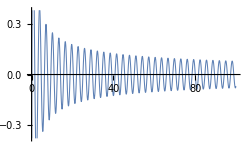

```mathematica
Plot[y[x]/.glif,{x,-100,100},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

7.  x^2 y''+x y'+1/4(x^2-1)y=0  (x=2z)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x^2 y''[x]+x y'[x]+1/4(x^2-1) y[x]==0}
```

{1/4 (-1+x^2) y[x]+x y'[x]+x^2 y''[x]==0}

```mathematica
e2=DSolve[e1,y[x],x,Assumptions->{x->2 z,x∈Reals}]
```

{{y[x]→(ⅇ^(-(ⅈ x)/2) C[1])/(√x)-(ⅈ ⅇ^((ⅈ x)/2) C[2])/(√x)}}

```mathematica
e3=ExpToTrig[e2]
```

{{y[x]→(C[1] Cos[x/2])/(√x)-(ⅈ C[2] Cos[x/2])/(√x)-(ⅈ C[1] Sin[x/2])/(√x)+(C[2] Sin[x/2])/(√x)}}

Mathematica gives the right answer, but includes imaginary elements, which, looking at the text answer, are not necessary.

```mathematica
e4=e3/.{-(ⅈ C[2] Cos[x/2])/(√x)->0,-(ⅈ C[1] Sin[x/2])/(√x)->0}
```

{{y[x]→(C[1] Cos[x/2])/(√x)+(C[2] Sin[x/2])/(√x)}}

```mathematica
e5=e4/.{C[1]->1,C[2]->1}
```

{{y[x]→Cos[x/2]/(√x)+Sin[x/2]/(√x)}}

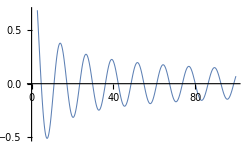

```mathematica
Plot[y[x]/.e5,{x,-100,100},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

9.  x y''+(2ν+1)y'+x y=0  (y=x^-ν u)

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x y''[x]+(2 ν+1)y'[x]+x y[x]==0}
```

{x y[x]+(1+2 ν) y'[x]+x y''[x]==0}

```mathematica
e2=DSolve[e1,y,x,Assumptions->{y[x]->x^-ν u}]
```

{{y→Function[{x},x^-ν BesselJ[ν,x] C[1]+x^-ν BesselY[ν,x] C[2]]}}

Mathematica’s answer checks.

```mathematica
e1/.e2//FullSimplify
```

{{True}}

The form of the above answer is not exactly the same as the text answer. They do not seem to be the same.

```mathematica
PossibleZeroQ[x^-ν BesselJ[ν,x] C[1]+x^-ν BesselY[ν,x] C[2]-(x^-ν BesselJ[ν,x] C[1]+x^-ν BesselJ[-ν,x] C[2])]
```

False

Manipulating the Mathematica answer for a plot.

```mathematica
e3=e2/.{C[1]->1,C[2]->1}
```

{{y[x]→x^-ν BesselJ[ν,x]+x^-ν BesselY[ν,x]}}

```mathematica
e4=Simplify[e3,Assumptions->ν∉Integers]
```

{{y[x]→x^-ν (BesselJ[ν,x]+BesselY[ν,x])}}

```mathematica
e5=e4/.ν->.5
```

{{y[x]→((0.7978845608028654 Cos[1.5708-x])/(√x)-(0.7978845608028654 Sin[1.5708-x])/(√x))/x^0.5}}

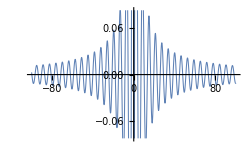

```mathematica
Plot[y[x]/.e5,{x,-100,100},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

19 - 25 Application of (21): deriviatives, integrals
Use the powerful formulas (21) to do problems 19 - 25.

23. Integration. Show that Integrate[x^2 J_0,x]=x^2 J_1[x]+x J_0[x]-Integrate[J_0[x],x]. (The last integral is nonelementary; tables exist, e.g. in reference [A13] in appendix 1.)

```mathematica
a1=Integrate[x^2 BesselJ[0,x],x]
```

1/3 x^3 HypergeometricPFQ[{3/2},{1,5/2},-x^2/4]

```mathematica
a2=x^2 BesselJ[1,x]
```

x^2 BesselJ[1,x]

```mathematica
a3=x BesselJ[0,x]
```

x BesselJ[0,x]

```mathematica
a4=Integrate[BesselJ[0,x],x]
```

x HypergeometricPFQ[{1/2},{1,3/2},-x^2/4]

```mathematica
PossibleZeroQ[a1-(a2+a3-a4)]
```

False

The demonstration fails. However, I don’t know if I expressed everything right.